Set::write: Tag Times in Null\ {{1, 15, 1, 15, 1}, {1, 15, 2, 15, 0}, {2, 14, 2, 15, 1}, {2, 14, 3, 15, 0}, {3, 13, 3, 15, 1}, {3, 13, 4, 13, 0}, {4, 12, 4, 13, 1}, {4, 14, 4, 14, 0}, {4, 15, 4, 15, 1}, {4, 15, 5, 15, 0}, {5, 11, 5, 15, 1}, {5, 11, 6, 11, 0}, {6, 10, 6, 11, 1}, {6, 12, 6, 14, 0}, {6, 15, 6, 15, 1}, {6, 15, 7, 11, 0}, {7, 9, 7, 11, 1}, « 17 », {11, 5, 11, 7, 1}, {11, 8, 11, 11, 0}, {11, 12, 11, 13, 1}, {11, 14, 11, 14, 0}, {11, 15, 11, 15, 1}, {11, 15, 12, 5, 0}, {12, 4, 12, 5, 1}, {12, 6, 12, 6, 0}, {12, 7, 12, 7, 1}, {12, 8, 12, 10, 0}, {12, 11, 12, 15, 1}, {12, 11, 13, 7, 0}, {13, 3, 13, 7, 1}, {13, 8, 13, 9, 0}, {13, 10, 13, 11, 1}, {13, 12, 13, 14, 0}, « 134 »} is Protected.

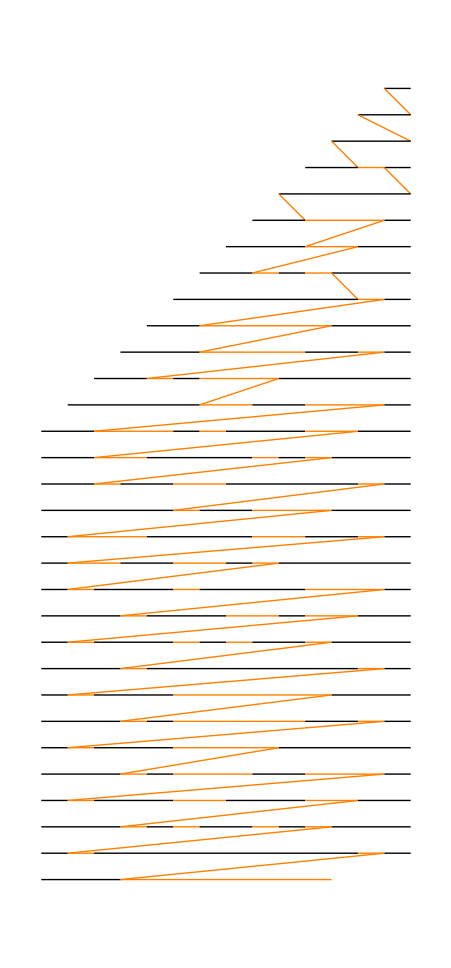

-Graphics-

```mathematica
list = Table[0, {30}];
list[[15]] = 1;
rules = {
{0,0,0} -> 0,
{0,0,1} -> 1, 
{0,1,0} -> 1, 
{0,1,1} -> 1, 
{1,0,0} -> 0, 
{1,0,1} -> 1,
{1,1,0} -> 1,
{1,1,1} -> 0
};
(*Chop up the list and apply the rules*)
Partition[list, 3, 1] /. rules;
(*Pad the list with zeros on both sides*)
Join[{0}, list, {0}];
(*Create a function to do this*)
step[seq_] := Join[{0}, Partition[seq, 3, 1] /. rules, {0}];
array = NestList[step, list, 30];

summarizedArray = {};

For[i = 1, i≤ Length[array], ++i,
	(* row i *)
	line = {};
	For[j=1, j≤ Length[array[[i]]], ++j,
		If[Length[line] == 0, (* init *)
			line = {i,j,i,j, array[[i,j]]}, 
		(*else: if value is the same as last line's value*)
			If[array[[i,j]] == line[[5]],
				line = {line[[1]], line[[2]], i,j, line[[5]]},
				(*else: new value --> store old line, start new line*)
				summarizedArray = Append[summarizedArray, line]; line = {i,j,i,j,array[[i,j]]}]
		]
	]
]
SubArrayToLine[a_] := (
	p1 = {a[[2]]-0.5, -a[[1]]};
	p2 = {a[[4]]+0.5, -a[[3]]};
	l = Line[{p1, p2}];
	Return[l];
)
FormattingOfLine[x_]:=(
	Return[ If[x == 0 , Orange, Black]];
)

FormatRawLineList[x_]:=(
	formattedLines = {};
	For[k = 1, k ≤ Length[x],++k,
		formattedLines = Append[formattedLines, FormattingOfLine[x[[k,5]]]];
		formattedLines = Append[formattedLines, SubArrayToLine[x[[k]]]];
	];
	Return[formattedLines];
)

RemoveTrailingZeroLines[x_]:=(
	indicesToBeDropped = {};
	(*first element*)
	If[ x[[1,5]]==0 , indicesToBeDropped=Append[indicesToBeDropped, {1}], 0]
	(* rest *)
	For[i=2,i≤Length[x]-1,++i,
		(*look at neighbors left and right, same y value? *)
		If[    (x[[i,5]] == 0 && x[[i,1]] ≠ x[[i-1,1]])       (* is zero-line and leading *)
			|| (x[[i,5]] == 0 && x[[i,1]] ≠ x[[i+1,1]]),       (* is zero-line and trailing *)
			indicesToBeDropped=Append[indicesToBeDropped, {i}],
			0]
	]
	(* last element *)
	If[Last[x][[5]]==0 , indicesToBeDropped = Append[indicesToBeDropped,{Length[x]}], 0];
	Return[Delete[x, indicesToBeDropped]]
	
)

AddRowStraddlingLines[x_]:=(
	resultList = {};
	For[i=1,i≤Length[x]-1,++i,
		resultList = Append[resultList, x[[i]]];
		If[x[[i,1]] ≠ x[[i+1,1]] && x[[i,5]] == 1 && x[[i+1,5]] == 1,   (* next line has different y-value *)
			tmp = x[[i]];   resultList = Append[resultList, {tmp[[1]], tmp[[2]], x[[i+1,3]], x[[i+1,4]], 0}],
			0];
	]
	resultList = Append[resultList, Last[x]];
	Return[resultList]
)

(*formattedLines = FormatRawLineList[summarizedArray];
Graphics[{ Thick, formattedLines}]*)
trimmed = RemoveTrailingZeroLines[summarizedArray];
a = AddRowStraddlingLines[trimmed];
formatted = FormatRawLineList[a];
Graphics[{ Thick, formatted}]
ArrayPlot[array]
```

```mathematica
{1,1,1,14,0}
```

{1,1,1,14,0}